```mathematica
fileName = "/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json";
RadioButtonBar[
Dynamic[fileName],
{
"/Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json",
"~/Downloads/optimizerHistory.json"
},Appearance->"Vertical"]
```

| /Users/nmajik/Documents/SLAC/FACET2-Bmad-PyTao/optimizerHistory.json
 | ~/Downloads/optimizerHistory.json

```mathematica
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];
```

```mathematica
(*Optional: Drop rows with non-numeric values*)
(*Length[raw]
raw = Select[raw,AllTrue[Values[#],NumericQ]&];
Length[raw]*)
```

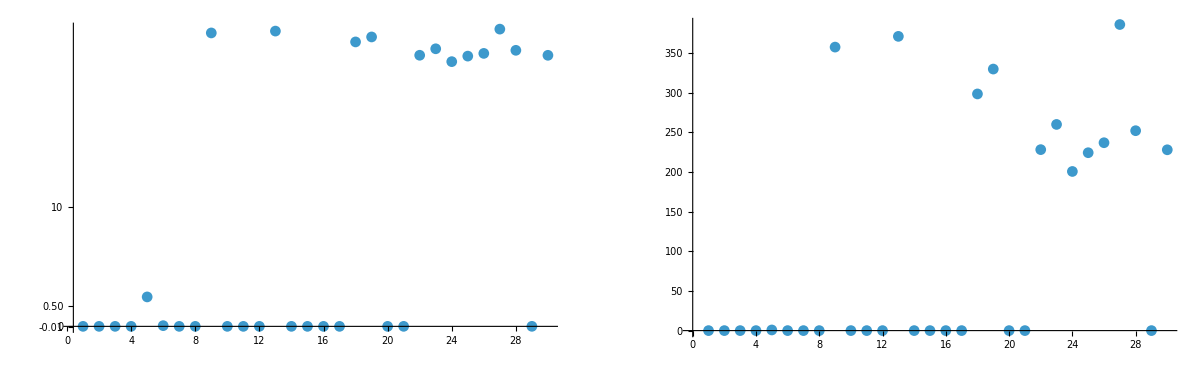

```mathematica
GraphicsGrid[{{
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600,
ScalingFunctions->"SignedLog"
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200]
```

### Live plot

```mathematica
(*Dynamic[livePlot]

makeLivePlot[]:=(
raw=Import[fileName];

raw= Association[#]&/@raw;
raw=Select[raw,NumericQ[#["maximizeMe"]]&];

livePlot = GraphicsGrid[{{
ListLogPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->All,
Joined->False,
ImageSize->600
],
ListPlot[
#["maximizeMe"]&/@raw,
(*PlotRange->All,*)
PlotRange->{0,All},
Joined->False,
ImageSize->600
]
}},ImageSize->1200];
)

task=CreateScheduledTask[makeLivePlot[],1]; (*Runs myFunction every 1 second*)
StartScheduledTask[task];*)
```

### Analyze

```mathematica
bestCase = MaximalBy[raw,#["maximizeMe"]&][[1]];
```

```mathematica
(*Format for yml*)
string = "";
Do[
string = string<>key<>" : "<>ToString[bestCase[key],CForm]<>"\n",
{key,Keys[bestCase]}
];
string
```

L1PhaseSet : -20.4203883213
L2PhaseSet : -35.113116249
L2EnergyOffset : -6.064810737519102e6
L3EnergyOffset : 1.5300726405061666e7
S1ELkG : 2098.8013910506
S2ELkG : -4008.838982962
S3ELkG : -1108.2642333891
S1EL_xOffset : 0.0009356044
S1EL_yOffset : 0.0001272276
S2EL_xOffset : -0.0004089369
S2EL_yOffset : 0.0001453551
S2ER_xOffset : -0.0001391335
S2ER_yOffset : -0.0014593892
S1ER_xOffset : 0.0013177564
S1ER_yOffset : -0.0011187153
PDrive_median_x : 0.0000482994
PDrive_median_y : 0.0000195257
PDrive_median_xp : -0.0000740396
PDrive_median_yp : -0.0001139549
PDrive_sigmaSI90_x : 0.0000235002
PDrive_sigmaSI90_y : 0.0000179997
PDrive_sigmaSI90_z : 0.0000154347
PDrive_sigmaSI90_xp : 0.0000745117
PDrive_sigmaSI90_yp : 0.0000518745
PDrive_emitSI90_x : 0.0000321873
PDrive_emitSI90_y : 0.0000127093
PDrive_norm_emit_x : 6.5367e-6
PDrive_norm_emit_y : 4.2728e-6
PDrive_zCentroid : 991.3317443091
PDrive_charge_nC : 1.20023904
PDrive_BMAG_x : 1.7462444478
PDrive_BMAG_y : 1.1174667885
PDrive_sliced_BMAG_x : List(4.4716066156,5.4136812036,3.8302530395,2.3238188852,2.4185677724)
PDrive_sliced_BMAG_y : List(1.0369526719,1.6639676455,1.9731317857,1.6288328321,1.0399624863)
PWitness_median_x : 0.0000389777
PWitness_median_y : 0.0000229648
PWitness_median_xp : 0.0001030768
PWitness_median_yp : -0.0002529117
PWitness_sigmaSI90_x : 0.000011115
PWitness_sigmaSI90_y : 0.0000137487
PWitness_sigmaSI90_z : 8.8074e-6
PWitness_sigmaSI90_xp : 0.0000587575
PWitness_sigmaSI90_yp : 0.0000707051
PWitness_emitSI90_x : 8.9598e-6
PWitness_emitSI90_y : 8.8375e-6
PWitness_norm_emit_x : 8.3086e-6
PWitness_norm_emit_y : 8.4309e-6
PWitness_zCentroid : 991.3319096503
PWitness_charge_nC : 0.40055904
PWitness_BMAG_x : 1.5856124363
PWitness_BMAG_y : 2.6166352203
PWitness_sliced_BMAG_x : List(1.32499524,1.6094963619,1.5840311024,1.6517155338,2.9419530806)
PWitness_sliced_BMAG_y : List(3.341106036,3.5412763241,3.555017218,3.4891730144,4.8917127259)
bunchSpacing : 0.0001653412
transverseCentroidOffset : 9.9359e-6
lostChargeFraction : 0.
errorTerm_lostChargeFraction : 0.
errorTerm_bunchSpacing : 0.
errorTerm_transverseOffset : 0.
errorTerm_angleOffset : 0.
errorTerm_mainObjective : 0.0204184639
errorTerm_secondaryObjective : 0.0003191627
maximizeMe : 385.7722070547
inputBeamFilePathSuffix : "/beams/2024-10-14_Impact_TwoBunch/2024-10-14_TwoBunch.h5"
csrTF : False

## Plot specific

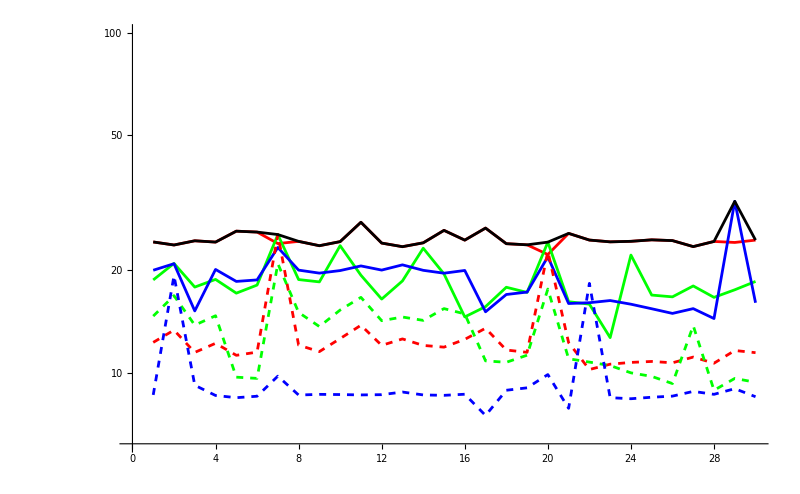

```mathematica
keys = {"PDrive_sigmaSI90_x","PDrive_sigmaSI90_y","PDrive_sigmaSI90_z","PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"};
ListLogPlot[
(10^6 raw[[All,#]]&/@keys)~Join~{(10^6 Max[#]&/@raw[[All,keys]])},
Joined->True,
ImageSize->800,
PlotStyle->{{Red},{Green},{Blue},{Red,Dashed},{Green,Dashed},{Blue,Dashed},{Black}},
InterpolationOrder->1,
PlotRange->{All,100}
]
(*ListPlot[
raw[[All,#]]&/@{"PWitness_sigmaSI90_x","PWitness_sigmaSI90_y","PWitness_sigmaSI90_z"},
Joined->True
]*)
```

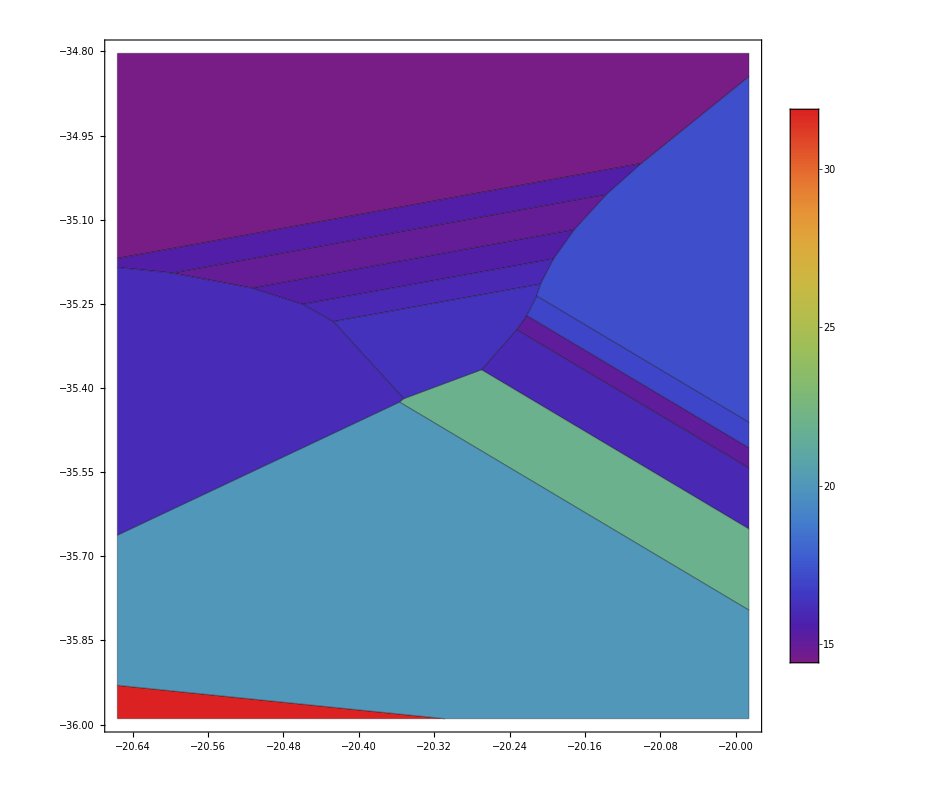

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6#["PDrive_sigmaSI90_z"]
(*10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]*)
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

```mathematica
ListDensityPlot[{
#["L1PhaseSet"],
#["L2PhaseSet"],
10^6 Max[{#["PDrive_sigmaSI90_z"],#["PWitness_sigmaSI90_z"]}]
}&/@raw,ImageSize->800,
ColorFunction->"Rainbow",InterpolationOrder->0,PlotRange->{All,50},Mesh->All,ColorFunction->"Rainbow",PlotLegends->Automatic]
```

-Graphics-

## Plot all

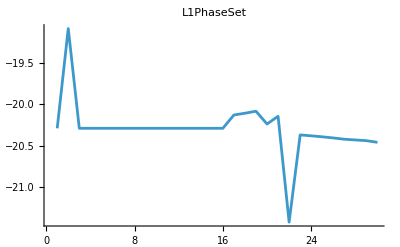
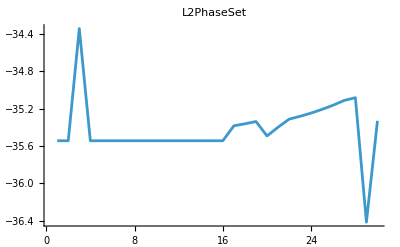
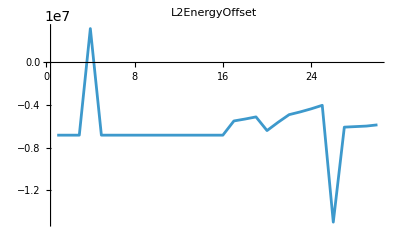
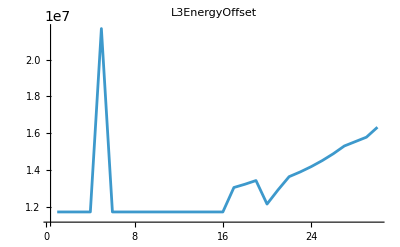
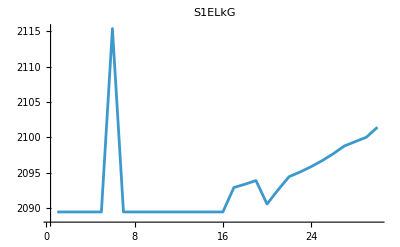
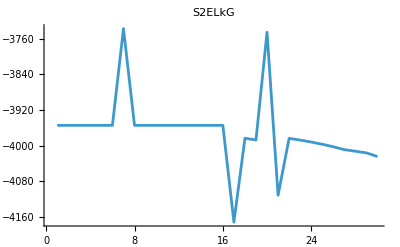
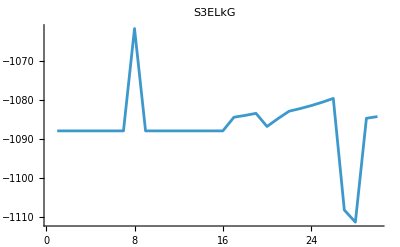
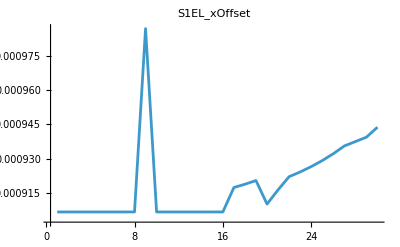
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | 0 | 0 | 0

```mathematica
imgArr=Table[
ListPlot[
raw[[All,key]],
PlotLabel->key,
ImageSize->400,
LabelStyle->15,
PlotRange->All,
Joined->True
],
{key,Keys[raw[[1]]]}
];

displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm
```

## Dump for symbolic regression

Open the CSV in excel, do the automatic suggestion, and resave

```mathematica
Export[
"~/srData.csv",
Dataset[raw]
]
```

~/srData.csv

## Linear model fit

```mathematica
freeVars=Intersection[
Keys[raw[[1]]],
{"QA10361kG","QA10371kG","QE10425kG","QE10441kG","QE10511kG","QE10525kG","L0BPhaseSet","L1PhaseSet","L2PhaseSet","L3PhaseSet","Q1EkG","Q2EkG","Q3EkG","Q4EkG","Q5EkG","Q6EkG","S1ELkG","S2ELkG","S3ELkG","S3ERkG","S2ERkG","S1ERkG","S1EL_xOffset","S1EL_yOffset","S2EL_xOffset","S2EL_yOffset","S2ER_xOffset","S2ER_yOffset","S1ER_xOffset","S1ER_yOffset","Q5FFkG","Q4FFkG","Q3FFkG","Q2FFkG","Q1FFkG","Q0FFkG", "XC1FFkG","XC3FFkG","YC1FFkG","YC2FFkG"}
]
(*Mathematica doesn't like underscores...*)
freeVarsMathematica=StringReplace[#,"_"->""]&/@freeVars;
```

{L1PhaseSet,L2PhaseSet,S1ELkG,S1EL_xOffset,S1EL_yOffset,S1ER_xOffset,S1ER_yOffset,S2ELkG,S2EL_xOffset,S2EL_yOffset,S2ER_xOffset,S2ER_yOffset,S3ELkG}

```mathematica
fitVar = "PDrive_twiss_beta_x"
(*fitVar = "bunchSpacing"*)
```

PDrive_twiss_beta_x

```mathematica
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
]
```

LinearModelFit::desmat: Unable to construct a numeric design matrix. Nominal variables may need to be specified, or non-numeric entries for numeric variables may need to be replaced.

LinearModelFit[{{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.0889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-34.3448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2115.38,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3737.31,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1061.71,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000986827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000211575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000308583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000196578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.0000879111,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00140817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00141233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00103826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1289,-35.3848,2092.94,0.000917494,0.000142242,0.001343,-0.0011076,-4171.43,-0.000377916,0.000127244,-0.000157244,-0.0014775,-1084.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1076,-35.3634,2093.4,0.000918916,0.000143664,0.00134442,-0.00110618,-3983.32,-0.000467161,0.000128666,-0.000155822,-0.00147608,-1083.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.0834,-35.3393,2093.92,0.000920528,0.000145276,0.00125536,-0.00110456,-3987.17,-0.000397638,0.000130278,-0.00015421,-0.00147447,-1083.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2373,-35.4932,2090.6,0.000910265,0.000135014,0.00131301,-0.00111483,-3745.55,-0.000410934,0.000120016,-0.000164473,-0.00148473,-1086.83,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1443,-35.4001,2092.61,0.00091647,0.000141218,0.00133875,-0.00110862,-4111.1,-0.000382594,0.00012622,-0.000158268,-0.00147852,-1084.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.4181,-35.3139,2094.47,0.000922218,0.000146966,0.00132454,-0.00110287,-3983.5,-0.000399469,0.000131969,-0.00015252,-0.00147278,-1082.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3686,-35.2831,2095.13,0.00092427,0.0000583518,0.0013235,-0.00110082,-3987.39,-0.00040092,0.000134021,-0.000150468,-0.00147072,-1082.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3792,-35.2482,2095.88,0.000926596,0.000128589,0.00132232,-0.00118916,-3991.79,-0.000402565,0.000136346,-0.000148142,-0.0014684,-1081.47,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3913,-35.2087,2096.74,0.000929232,0.000128191,0.00132098,-0.00111862,-3996.78,-0.00040443,0.000138982,-0.000145506,-0.00146576,-1080.61,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4049,-35.1639,2097.71,0.000932219,0.000127739,0.00131947,-0.00111866,-4002.43,-0.000406542,0.00014197,-0.000142519,-0.00146277,-1079.63,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4204,-35.1131,2098.8,0.000935604,0.000127228,0.00131776,-0.00111872,-4008.84,-0.000408937,0.000145355,-0.000139134,-0.00145939,-1108.26,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4292,-35.0843,2099.42,0.000937523,0.000126938,0.00131678,-0.00111875,-4012.47,-0.000410294,0.000147274,-0.000137215,-0.00145747,-1111.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4379,-36.4156,2100.04,0.000939441,0.000126648,0.00131581,-0.00111878,-4016.1,-0.000411651,0.000149192,-0.000135297,-0.00145555,-1084.72,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4578,-35.3317,2101.45,0.00094379,0.000125991,0.00131361,-0.00111884,-4024.33,-0.000414727,0.0000628741,-0.000130948,-0.0014512,-1084.29,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG}]

```mathematica
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
AspectRatio->Automatic,
Frame->True,
FrameLabel->{"Actual","Predicted"}
]
```

-Graphics-

```mathematica
lm["ANOVATable"]
```

LinearModelFit[{{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-19.0889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-34.3448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2115.38,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3737.31,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1061.71,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000986827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000211575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000308583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000196578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.0000879111,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00140817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00141233,-0.00111826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2889,-35.5448,2089.48,0.000906827,0.000131575,0.00133233,-0.00103826,-3954.37,-0.000388583,0.000116578,-0.000167911,-0.00148817,-1087.96,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1289,-35.3848,2092.94,0.000917494,0.000142242,0.001343,-0.0011076,-4171.43,-0.000377916,0.000127244,-0.000157244,-0.0014775,-1084.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1076,-35.3634,2093.4,0.000918916,0.000143664,0.00134442,-0.00110618,-3983.32,-0.000467161,0.000128666,-0.000155822,-0.00147608,-1083.99,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.0834,-35.3393,2093.92,0.000920528,0.000145276,0.00125536,-0.00110456,-3987.17,-0.000397638,0.000130278,-0.00015421,-0.00147447,-1083.46,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.2373,-35.4932,2090.6,0.000910265,0.000135014,0.00131301,-0.00111483,-3745.55,-0.000410934,0.000120016,-0.000164473,-0.00148473,-1086.83,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.1443,-35.4001,2092.61,0.00091647,0.000141218,0.00133875,-0.00110862,-4111.1,-0.000382594,0.00012622,-0.000158268,-0.00147852,-1084.79,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-21.4181,-35.3139,2094.47,0.000922218,0.000146966,0.00132454,-0.00110287,-3983.5,-0.000399469,0.000131969,-0.00015252,-0.00147278,-1082.91,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3686,-35.2831,2095.13,0.00092427,0.0000583518,0.0013235,-0.00110082,-3987.39,-0.00040092,0.000134021,-0.000150468,-0.00147072,-1082.23,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3792,-35.2482,2095.88,0.000926596,0.000128589,0.00132232,-0.00118916,-3991.79,-0.000402565,0.000136346,-0.000148142,-0.0014684,-1081.47,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.3913,-35.2087,2096.74,0.000929232,0.000128191,0.00132098,-0.00111862,-3996.78,-0.00040443,0.000138982,-0.000145506,-0.00146576,-1080.61,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4049,-35.1639,2097.71,0.000932219,0.000127739,0.00131947,-0.00111866,-4002.43,-0.000406542,0.00014197,-0.000142519,-0.00146277,-1079.63,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4204,-35.1131,2098.8,0.000935604,0.000127228,0.00131776,-0.00111872,-4008.84,-0.000408937,0.000145355,-0.000139134,-0.00145939,-1108.26,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4292,-35.0843,2099.42,0.000937523,0.000126938,0.00131678,-0.00111875,-4012.47,-0.000410294,0.000147274,-0.000137215,-0.00145747,-1111.37,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4379,-36.4156,2100.04,0.000939441,0.000126648,0.00131581,-0.00111878,-4016.1,-0.000411651,0.000149192,-0.000135297,-0.00145555,-1084.72,Missing[KeyAbsent,PDrive_twiss_beta_x]},{-20.4578,-35.3317,2101.45,0.00094379,0.000125991,0.00131361,-0.00111884,-4024.33,-0.000414727,0.0000628741,-0.000130948,-0.0014512,-1084.29,Missing[KeyAbsent,PDrive_twiss_beta_x]}},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG},{L1PhaseSet,L2PhaseSet,S1ELkG,S1ELxOffset,S1ELyOffset,S1ERxOffset,S1ERyOffset,S2ELkG,S2ELxOffset,S2ELyOffset,S2ERxOffset,S2ERyOffset,S3ELkG}][ANOVATable]

### Fit all dependent vars

```mathematica
allFitVars  = Complement[
Keys[raw[[1]]],
freeVars
];
```

```mathematica
(*
imgArr=Table[
lmData = designMatrix = Table[
row[#]&/@(Append[freeVars,fitVar]),
{row,raw}
];
lm =LinearModelFit[
lmData,
Symbol[#]&/@freeVarsMathematica,
Symbol[#]&/@freeVarsMathematica
];

Show[
ListPlot[
Transpose[
{
lm["Response"],
lm["PredictedResponse"]
}
],
Frame->True,
FrameLabel->{"Actual","Predicted"},
PlotLabel->Row[{fitVar,": ",Style[ToString[lm["RSquared"]],ColorData["Rainbow"][lm["RSquared"]]]}],
ImageSize->400,
AspectRatio->1,
LabelStyle->15,
PlotRange->All
],
Plot[x,{x,Min[lm["Response"]],Max[lm["Response"]]},PlotStyle->Red]
],
{fitVar,allFitVars}
];*)
```

```mathematica
(*displayCols = 4;
ArrayReshape[
imgArr,{Ceiling[Length[imgArr]/displayCols],displayCols}
]//TableForm*)
```

## Parse JSON strings to assoc

```mathematica
(*This is a stupid trick, but ensures numbers in scientific notation are interpreted correctly: https://mathematica.stackexchange.com/questions/15051/reading-in-scientific-notation-from-c-to-mathematica*)
stringToNumber[string_]:=ImportString[string,"Table"][[1,1]]
```

```mathematica
jsonTextToAssoc[string_]:=(
stringParts = StringSplit[StringDelete[#,WhitespaceCharacter],":"]&/@StringSplit[string,"\n"];
Association[#[[1]]->stringToNumber[#[[2]]]&/@stringParts]
)
```

```mathematica
tmp="L0BPhaseSet : -1.7210344516
L1PhaseSet : -20.3120443443
L2PhaseSet : -38.6737055166
L3PhaseSet : -1.4632882388
S1EL_xOffset : 0.0003852549
S1EL_yOffset : -0.0002411137
S2EL_xOffset : -0.0014178669
S2EL_yOffset : 0.0000111705
S2ER_xOffset : -0.002238162
S2ER_yOffset : -0.0006759962
S1ER_xOffset : 0.0010071369
S1ER_yOffset : 0.0003984557
XC1FFkG : 0.2064553639
XC3FFkG : -0.089916372
YC1FFkG : -0.0022311951
YC2FFkG : -0.0085115845";
```

```mathematica
priorSettings = jsonTextToAssoc[tmp]
```

<|L0BPhaseSet→-1.72103,L1PhaseSet→-20.312,L2PhaseSet→-38.6737,L3PhaseSet→-1.46329,S1EL_xOffset→0.000385255,S1EL_yOffset→-0.000241114,S2EL_xOffset→-0.00141787,S2EL_yOffset→0.0000111705,S2ER_xOffset→-0.00223816,S2ER_yOffset→-0.000675996,S1ER_xOffset→0.00100714,S1ER_yOffset→0.000398456,XC1FFkG→0.206455,XC3FFkG→-0.0899164,YC1FFkG→-0.0022312,YC2FFkG→-0.00851158|>

```mathematica
TableForm[
Table[
{
key,priorSettings[key],bestCase[key],bestCase[key]-priorSettings[key]
},
{key,Keys[priorSettings]}
],
TableHeadings->{None,{
Style["Parameter",Bold],
Style["150 μm spacing",Bold],
Style["New spacing",Bold],
Style["Delta",Bold]}}
]
```

Parameter | 150 μm spacing | New spacing | Delta
L0BPhaseSet | -1.72103 | Missing[KeyAbsent,L0BPhaseSet] | 1.72103+Missing[KeyAbsent,L0BPhaseSet]
L1PhaseSet | -20.312 | -20.4204 | -0.108344
L2PhaseSet | -38.6737 | -35.1131 | 3.56059
L3PhaseSet | -1.46329 | Missing[KeyAbsent,L3PhaseSet] | 1.46329+Missing[KeyAbsent,L3PhaseSet]
S1EL_xOffset | 0.000385255 | 0.000935604 | 0.00055035
S1EL_yOffset | -0.000241114 | 0.000127228 | 0.000368341
S2EL_xOffset | -0.00141787 | -0.000408937 | 0.00100893
S2EL_yOffset | 0.0000111705 | 0.000145355 | 0.000134185
S2ER_xOffset | -0.00223816 | -0.000139134 | 0.00209903
S2ER_yOffset | -0.000675996 | -0.00145939 | -0.000783393
S1ER_xOffset | 0.00100714 | 0.00131776 | 0.00031062
S1ER_yOffset | 0.000398456 | -0.00111872 | -0.00151717
XC1FFkG | 0.206455 | Missing[KeyAbsent,XC1FFkG] | -0.206455+Missing[KeyAbsent,XC1FFkG]
XC3FFkG | -0.0899164 | Missing[KeyAbsent,XC3FFkG] | 0.0899164+Missing[KeyAbsent,XC3FFkG]
YC1FFkG | -0.0022312 | Missing[KeyAbsent,YC1FFkG] | 0.0022312+Missing[KeyAbsent,YC1FFkG]
YC2FFkG | -0.00851158 | Missing[KeyAbsent,YC2FFkG] | 0.00851158+Missing[KeyAbsent,YC2FFkG]